```mathematica
ivp:=NDSolve[{x1'[t]==2x1[t]-x1[t]^2-x1[t]*x2[t],x2'[t]==3x2[t]-2x1[t]*x2[t]-x2[t]^2,x1[0]==1,x2[0]==5,x1'[0]==0,x2'[0]==0},{x1[t],x2[t]},{t,0,2}]
VectorPlot[{x1, x2}, {x1, -3, 3}, {x2, -3, 3}]
StreamPlot[{x1, x2}, {x1, -3, 3}, {x2, -3, 3}]
```

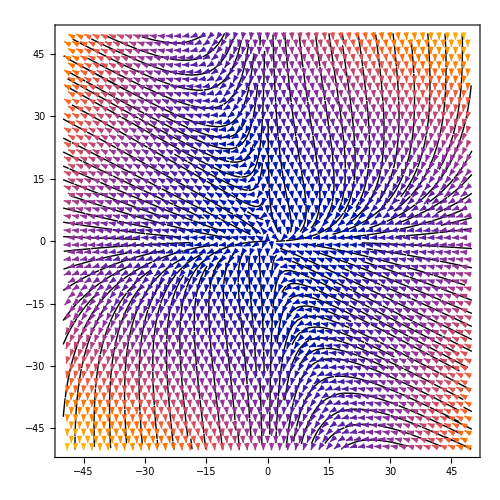

```mathematica
StreamPlot[{2x-x^2+x*y, 3y-2x*y-y^2}, {x, -50, 50}, {y, -50,
   50}, VectorPoints -> 50, StreamPoints -> Fine, 
 StreamColorFunction -> None, StreamStyle -> {Black, "Segment"}, 
 AspectRatio -> Automatic, ImageSize -> 500]
```

```mathematica
D[(2x-x^2+x*y), x]/.x->0/.y->0
D[(2x-x^2+x*y), y]/.x->0/.y->0
D[(3y-2x*y-y^2), x]/.x->0/.y->0
D[(3y-2x*y-y^2), y]/.x->0/.y->0
```

2

0

0

3

```mathematica
J={{D[(2x-x^2+x*y), x]/.x->0/.y->0,D[(2x-x^2+x*y), y]/.x->0/.y->0},{D[(3y-2x*y-y^2), x]/.x->0/.y->0,D[(3y-2x*y-y^2), y]/.x->0/.y->0}}
```

{{2,0},{0,3}}